# 1g and 1u eigenvalues

## 1g

```mathematica
Clear[R,C3,Δ]

matrix={{-2*C3/R^3-Δ/3,Δ/3,Δ/3},{Δ/3,-C3/R^3-Δ/3,-Δ/3},{Δ/3,-Δ/3,C3/R^3-Δ/3}};

charPoly=CharacteristicPolynomial[matrix,λ];

eigenvalues=Solve[charPoly==0,λ]
```

{{λ→(-2 C3-R^3 Δ)/(3 R^3)+(2^(1/3) (-(7 C3^2)/R^6-Δ^2))/(3 (-(20 C3^3)/R^9+2 Δ^3+√(4 (-(7 C3^2)/R^6-Δ^2)^3+(-(20 C3^3)/R^9+2 Δ^3)^2))^(1/3))-((-(20 C3^3)/R^9+2 Δ^3+√(4 (-(7 C3^2)/R^6-Δ^2)^3+(-(20 C3^3)/R^9+2 Δ^3)^2))^(1/3))/(3 2^(1/3))},{λ→(-2 C3-R^3 Δ)/(3 R^3)-((1+ⅈ √3) (-(7 C3^2)/R^6-Δ^2))/(3 2^(2/3) (-(20 C3^3)/R^9+2 Δ^3+√(4 (-(7 C3^2)/R^6-Δ^2)^3+(-(20 C3^3)/R^9+2 Δ^3)^2))^(1/3))+((1-ⅈ √3) (-(20 C3^3)/R^9+2 Δ^3+√(4 (-(7 C3^2)/R^6-Δ^2)^3+(-(20 C3^3)/R^9+2 Δ^3)^2))^(1/3))/(6 2^(1/3))},{λ→(-2 C3-R^3 Δ)/(3 R^3)-((1-ⅈ √3) (-(7 C3^2)/R^6-Δ^2))/(3 2^(2/3) (-(20 C3^3)/R^9+2 Δ^3+√(4 (-(7 C3^2)/R^6-Δ^2)^3+(-(20 C3^3)/R^9+2 Δ^3)^2))^(1/3))+((1+ⅈ √3) (-(20 C3^3)/R^9+2 Δ^3+√(4 (-(7 C3^2)/R^6-Δ^2)^3+(-(20 C3^3)/R^9+2 Δ^3)^2))^(1/3))/(6 2^(1/3))}}

```mathematica
(-2 C3-R^3 Δ)/(3 R^3)+(2^(1/3) (Δ^2))/(3 (2 Δ^3+√(4 (-Δ^2)^3))^(1/3))-((+2 Δ^3+√(4 (Δ^2)^3+(2 Δ^3)^2))^(1/3))/(3 2^(1/3))
```

```mathematica
Simplify[(-2 C3-R^3 Δ)/(3 R^3)+(2^(1/3) (Δ^2))/(3 (2 Δ^3+√(4 (-Δ^2)^3))^(1/3))-((+2 Δ^3+√(4 (Δ^2)^3+(2 Δ^3)^2))^(1/3))/(3 2^(1/3))]
```

```mathematica
1/3 (-(2 C3)/R^3-Δ+Δ^2/((Δ^3+√(Δ^6))^(1/3))-(Δ^3+√2 √(Δ^6))^(1/3))
```

```mathematica
Clear[R,C3,Δ]

eigenvalue1=(-2 C3-R^3 Δ)/(3 R^3)+(2^(1/3) (-(7 C3^2)/R^6-Δ^2))/(3 (-(20 C3^3)/R^9+2 Δ^3+√(4 (-(7 C3^2)/R^6-Δ^2)^3+(-(20 C3^3)/R^9+2 Δ^3)^2))^(1/3))-((-(20 C3^3)/R^9+2 Δ^3+√(4 (-(7 C3^2)/R^6-Δ^2)^3+(-(20 C3^3)/R^9+2 Δ^3)^2))^(1/3))/(3 2^(1/3))

taylorExpansion=Series[eigenvalue1,{Δ,0,1}]//Normal
```

(-2 C3-R^3 Δ)/(3 R^3)+(2^(1/3) (-(7 C3^2)/R^6-Δ^2))/(3 (-(20 C3^3)/R^9+2 Δ^3+√(4 (-(7 C3^2)/R^6-Δ^2)^3+(-(20 C3^3)/R^9+2 Δ^3)^2))^(1/3))-((-(20 C3^3)/R^9+2 Δ^3+√(4 (-(7 C3^2)/R^6-Δ^2)^3+(-(20 C3^3)/R^9+2 Δ^3)^2))^(1/3))/(3 2^(1/3))

-(2 C3)/(3 R^3)-(7 C3^2)/(3 R^6 ((-10 C3^3+9 √3 √(-C3^6/R^18) R^9)/R^9)^(1/3))-1/3 ((-10 C3^3+9 √3 √(-C3^6/R^18) R^9)/R^9)^(1/3)-Δ/3

```mathematica
eigenvalue1_simp=-((2 C3)/(3 R^3))-(7 C3^2)/(3 R^6 ((-10 C3^3)/R^9)^(1/3))-1/3 ((-10 C3^3)/R^9)^(1/3)-Δ/3
```

-1/3 10^(1/3) (-C3^3/R^9)^(1/3)-(7 C3^2)/(3 10^(1/3) (-C3^3/R^9)^(1/3) R^6)-(2 C3)/(3 R^3)-Δ/3

```mathematica
Clear[R,C3,Δ]

eigenvalue2=(-2 C3-R^3 Δ)/(3 R^3)-((1+ⅈ √3) (-(7 C3^2)/R^6-Δ^2))/(3 2^(2/3) (-(20 C3^3)/R^9+2 Δ^3+√(4 (-(7 C3^2)/R^6-Δ^2)^3+(-(20 C3^3)/R^9+2 Δ^3)^2))^(1/3))+((1-ⅈ √3) (-(20 C3^3)/R^9+2 Δ^3+√(4 (-(7 C3^2)/R^6-Δ^2)^3+(-(20 C3^3)/R^9+2 Δ^3)^2))^(1/3))/(6 2^(1/3))

taylorExpansion=Series[eigenvalue2,{Δ,0,1}]//Normal
```

(-2 C3-R^3 Δ)/(3 R^3)-((1+ⅈ √3) (-(7 C3^2)/R^6-Δ^2))/(3 2^(2/3) (-(20 C3^3)/R^9+2 Δ^3+√(4 (-(7 C3^2)/R^6-Δ^2)^3+(-(20 C3^3)/R^9+2 Δ^3)^2))^(1/3))+((1-ⅈ √3) (-(20 C3^3)/R^9+2 Δ^3+√(4 (-(7 C3^2)/R^6-Δ^2)^3+(-(20 C3^3)/R^9+2 Δ^3)^2))^(1/3))/(6 2^(1/3))

-(2 C3)/(3 R^3)+(7 (1+ⅈ √3) C3^2)/(6 R^6 ((-10 C3^3+9 √3 √(-C3^6/R^18) R^9)/R^9)^(1/3))+1/6 (1-ⅈ √3) ((-10 C3^3+9 √3 √(-C3^6/R^18) R^9)/R^9)^(1/3)-Δ/3

```mathematica
eigenvalue2_simp=-(2 C3)/(3 R^3)+(7 (1+ⅈ √3) C3^2)/(6 R^6 ((-10 C3^3)/R^9)^(1/3))+1/6 (1-ⅈ √3) ((-10 C3^3)/R^9)^(1/3)-Δ/3
```

(5^(1/3) (1-ⅈ √3) (-C3^3/R^9)^(1/3))/(3 2^(2/3))+(7 (1+ⅈ √3) C3^2)/(6 10^(1/3) (-C3^3/R^9)^(1/3) R^6)-(2 C3)/(3 R^3)-Δ/3

```mathematica
(5^(1/3) (-C3/R^3))/(3 2^(2/3))+(7  C3)/(6 10^(1/3)  R^3)-(2 C3)/(3 R^3)-Δ/3
```

```mathematica
Clear[R,C3,Δ]

eigenvalue3=(-2 C3-R^3 Δ)/(3 R^3)-((1-ⅈ √3) (-(7 C3^2)/R^6-Δ^2))/(3 2^(2/3) (-(20 C3^3)/R^9+2 Δ^3+√(4 (-(7 C3^2)/R^6-Δ^2)^3+(-(20 C3^3)/R^9+2 Δ^3)^2))^(1/3))+((1+ⅈ √3) (-(20 C3^3)/R^9+2 Δ^3+√(4 (-(7 C3^2)/R^6-Δ^2)^3+(-(20 C3^3)/R^9+2 Δ^3)^2))^(1/3))/(6 2^(1/3))

taylorExpansion=Series[eigenvalue3,{Δ,0,1}]//Normal
```

(-2 C3-R^3 Δ)/(3 R^3)-((1-ⅈ √3) (-(7 C3^2)/R^6-Δ^2))/(3 2^(2/3) (-(20 C3^3)/R^9+2 Δ^3+√(4 (-(7 C3^2)/R^6-Δ^2)^3+(-(20 C3^3)/R^9+2 Δ^3)^2))^(1/3))+((1+ⅈ √3) (-(20 C3^3)/R^9+2 Δ^3+√(4 (-(7 C3^2)/R^6-Δ^2)^3+(-(20 C3^3)/R^9+2 Δ^3)^2))^(1/3))/(6 2^(1/3))

-(2 C3)/(3 R^3)+(7 (1-ⅈ √3) C3^2)/(6 R^6 ((-10 C3^3+9 √3 √(-C3^6/R^18) R^9)/R^9)^(1/3))+1/6 (1+ⅈ √3) ((-10 C3^3+9 √3 √(-C3^6/R^18) R^9)/R^9)^(1/3)-Δ/3

```mathematica
-(2 C3)/(3 R^3)+(7 (-√3) C3)/(6 R^3 (10 )^(1/3))+1/6 (- √3) C3/R^3(10)^(1/3)-Δ/3
```

## 1u

```mathematica
Clear[R,C3,Δ]

matrix={{2*C3/R^3-Δ/3,Δ/3,Δ/3},{Δ/3,C3/R^3-Δ/3,-Δ/3},{Δ/3,-Δ/3,-C3/R^3-Δ/3}};

charPoly=CharacteristicPolynomial[matrix,λ];

eigenvalues=Solve[charPoly==0,λ]
```

{{λ→(2 C3-R^3 Δ)/(3 R^3)+(2^(1/3) (-(7 C3^2)/R^6-Δ^2))/(3 ((20 C3^3)/R^9+2 Δ^3+√(4 (-(7 C3^2)/R^6-Δ^2)^3+((20 C3^3)/R^9+2 Δ^3)^2))^(1/3))-(((20 C3^3)/R^9+2 Δ^3+√(4 (-(7 C3^2)/R^6-Δ^2)^3+((20 C3^3)/R^9+2 Δ^3)^2))^(1/3))/(3 2^(1/3))},{λ→(2 C3-R^3 Δ)/(3 R^3)-((1+ⅈ √3) (-(7 C3^2)/R^6-Δ^2))/(3 2^(2/3) ((20 C3^3)/R^9+2 Δ^3+√(4 (-(7 C3^2)/R^6-Δ^2)^3+((20 C3^3)/R^9+2 Δ^3)^2))^(1/3))+((1-ⅈ √3) ((20 C3^3)/R^9+2 Δ^3+√(4 (-(7 C3^2)/R^6-Δ^2)^3+((20 C3^3)/R^9+2 Δ^3)^2))^(1/3))/(6 2^(1/3))},{λ→(2 C3-R^3 Δ)/(3 R^3)-((1-ⅈ √3) (-(7 C3^2)/R^6-Δ^2))/(3 2^(2/3) ((20 C3^3)/R^9+2 Δ^3+√(4 (-(7 C3^2)/R^6-Δ^2)^3+((20 C3^3)/R^9+2 Δ^3)^2))^(1/3))+((1+ⅈ √3) ((20 C3^3)/R^9+2 Δ^3+√(4 (-(7 C3^2)/R^6-Δ^2)^3+((20 C3^3)/R^9+2 Δ^3)^2))^(1/3))/(6 2^(1/3))}}

```mathematica
Clear[R,C3,Δ]

eigenvalue1u=(-2 C3-R^3 Δ)/(3 R^3)+(2^(1/3) (-(7 C3^2)/R^6-Δ^2))/(3 (-(20 C3^3)/R^9+2 Δ^3+√(4 (-(7 C3^2)/R^6-Δ^2)^3+(-(20 C3^3)/R^9+2 Δ^3)^2))^(1/3))-((-(20 C3^3)/R^9+2 Δ^3+√(4 (-(7 C3^2)/R^6-Δ^2)^3+(-(20 C3^3)/R^9+2 Δ^3)^2))^(1/3))/(3 2^(1/3))

taylorExpansion=Series[eigenvalue1u,{Δ,0,1}]//Normal
```

(-2 C3-R^3 Δ)/(3 R^3)+(2^(1/3) (-(7 C3^2)/R^6-Δ^2))/(3 (-(20 C3^3)/R^9+2 Δ^3+√(4 (-(7 C3^2)/R^6-Δ^2)^3+(-(20 C3^3)/R^9+2 Δ^3)^2))^(1/3))-((-(20 C3^3)/R^9+2 Δ^3+√(4 (-(7 C3^2)/R^6-Δ^2)^3+(-(20 C3^3)/R^9+2 Δ^3)^2))^(1/3))/(3 2^(1/3))

-(2 C3)/(3 R^3)-(7 C3^2)/(3 R^6 ((-10 C3^3+9 √3 √(-C3^6/R^18) R^9)/R^9)^(1/3))-1/3 ((-10 C3^3+9 √3 √(-C3^6/R^18) R^9)/R^9)^(1/3)-Δ/3

```mathematica
-(2 C3)/(3 R^3)-(7 C3)/(3 R^3 (10 )^(1/3))-C3/(3 R^3) (10)^(1/3)-Δ/3
```

```mathematica
Clear[R,C3,Δ]

eigenvalue2u=(2 C3-R^3 Δ)/(3 R^3)-((1+ⅈ √3) (-(7 C3^2)/R^6-Δ^2))/(3 2^(2/3) ((20 C3^3)/R^9+2 Δ^3+√(4 (-(7 C3^2)/R^6-Δ^2)^3+((20 C3^3)/R^9+2 Δ^3)^2))^(1/3))+((1-ⅈ √3) ((20 C3^3)/R^9+2 Δ^3+√(4 (-(7 C3^2)/R^6-Δ^2)^3+((20 C3^3)/R^9+2 Δ^3)^2))^(1/3))/(6 2^(1/3))

taylorExpansion=Series[eigenvalue2u,{Δ,0,1}]//Normal
```

(2 C3-R^3 Δ)/(3 R^3)-((1+ⅈ √3) (-(7 C3^2)/R^6-Δ^2))/(3 2^(2/3) ((20 C3^3)/R^9+2 Δ^3+√(4 (-(7 C3^2)/R^6-Δ^2)^3+((20 C3^3)/R^9+2 Δ^3)^2))^(1/3))+((1-ⅈ √3) ((20 C3^3)/R^9+2 Δ^3+√(4 (-(7 C3^2)/R^6-Δ^2)^3+((20 C3^3)/R^9+2 Δ^3)^2))^(1/3))/(6 2^(1/3))

(2 C3)/(3 R^3)+(7 (1+ⅈ √3) C3^2)/(6 R^6 ((10 C3^3+9 √3 √(-C3^6/R^18) R^9)/R^9)^(1/3))+1/6 (1-ⅈ √3) ((10 C3^3+9 √3 √(-C3^6/R^18) R^9)/R^9)^(1/3)-Δ/3

```mathematica
(2 C3)/(3 R^3)+(7  C3)/(6 R^3 (10 )^(1/3))+1/6  C3/R^3(10 )^(1/3)-Δ/3
```

```mathematica
Clear[R,C3,Δ]

eigenvalue3u=(-2 C3-R^3 Δ)/(3 R^3)-((1-ⅈ √3) (-(7 C3^2)/R^6-Δ^2))/(3 2^(2/3) (-(20 C3^3)/R^9+2 Δ^3+√(4 (-(7 C3^2)/R^6-Δ^2)^3+(-(20 C3^3)/R^9+2 Δ^3)^2))^(1/3))+((1+ⅈ √3) (-(20 C3^3)/R^9+2 Δ^3+√(4 (-(7 C3^2)/R^6-Δ^2)^3+(-(20 C3^3)/R^9+2 Δ^3)^2))^(1/3))/(6 2^(1/3))

taylorExpansion=Series[eigenvalue3u,{Δ,0,1}]//Normal
```

(-2 C3-R^3 Δ)/(3 R^3)-((1-ⅈ √3) (-(7 C3^2)/R^6-Δ^2))/(3 2^(2/3) (-(20 C3^3)/R^9+2 Δ^3+√(4 (-(7 C3^2)/R^6-Δ^2)^3+(-(20 C3^3)/R^9+2 Δ^3)^2))^(1/3))+((1+ⅈ √3) (-(20 C3^3)/R^9+2 Δ^3+√(4 (-(7 C3^2)/R^6-Δ^2)^3+(-(20 C3^3)/R^9+2 Δ^3)^2))^(1/3))/(6 2^(1/3))

-(2 C3)/(3 R^3)+(7 (1-ⅈ √3) C3^2)/(6 R^6 ((-10 C3^3+9 √3 √(-C3^6/R^18) R^9)/R^9)^(1/3))+1/6 (1+ⅈ √3) ((-10 C3^3+9 √3 √(-C3^6/R^18) R^9)/R^9)^(1/3)-Δ/3

```mathematica
-(2 C3)/(3 R^3)+(7 (-√3) C3)/(6 R^3 (10 )^(1/3))+1/6 C3/R^3(-√3) (10 )^(1/3)-Δ/3
```

# Perturbation theory

```mathematica
(*Define unperturbed Hamiltonian*)
H0={{-2*C3/R^3,0,0},{0,-C3/R^3,0},{0,0,C3/R^3}};

(*Find the eigenvectors of H0*)
eigenvalues=Eigenvalues[H0];
H1={{-δ/3,δ/3,δ/3},{δ/3,-δ/3,-δ/3},{δ/3,-δ/3,-δ/3}};
E2=Table[Sum[(H1[[i,j]]*H1[[j,k]])/(E0[[i]]-E0[[j]]),{j,1,3},{k,1,3}],{i,1,3}];

(*Display second-order corrections to the energies*)
E2
```

```mathematica
(*Define the perturbation matrix H1 and unperturbed eigenstates and eigenvalues*)H1={{a,b,c},{d,e,f},{g,h,i}};
Eigenstates={}; (*Define the unperturbed eigenstates*)
Eigenvalues0={}; (*Define the unperturbed eigenvalues*)

(*Calculate the second-order corrections to the energy*)
E2=Table[Sum[If[i!=j,(H1[[i,k]]*H1[[k,j]])/(Eigenvalues0[[i]]-Eigenvalues0[[j]]),0],{k,1,3}],{i,1,3},{j,1,3}]

(*Display the second-order corrections to the energy*)
E2
```

```mathematica
(*Define the unperturbed Hamiltonian H0*)H0={{E0,0},{0,E0}};

(*Define the perturbation matrix H1*)
H1={{δ,0},{0,-δ}};

(*Define the unperturbed eigenvalues*)
Eigenvalues0={E0,E0};

(*Calculate the second-order corrections to the energy*)
E2=Table[Sum[If[i!=j,(H1[[i,k]]*H1[[k,j]])/(Eigenvalues0[[i]]-Eigenvalues0[[j]]),0],{k,1,2}],{i,1,2},{j,1,2}];

(*Display the second-order corrections to the energy*)
E2
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{{0,Indeterminate},{Indeterminate,0}}

```mathematica
(*Define the unperturbed Hamiltonian H0*)H0={{E0,0},{0,E0}};

(*Define the perturbation matrix H1*)
H1={{δ,0},{0,-δ}};

(*Define the unperturbed eigenvalues*)
Eigenvalues0={E0,E0};

(*Calculate the second-order corrections to the energy*)
E2=Table[0,{2},{2}];

(*Display the second-order corrections to the energy*)
E2
```

{{0,0},{0,0}}

```mathematica
(*Define the unperturbed Hamiltonian H0*)E0=1; (*Unperturbed energy*)
H0={{E0,0},{0,E0}};

(*Define the perturbation matrix H1*)
δ=0.1; (*Perturbation strength*)
H1={{0,δ},{δ,0}};

(*Define the unperturbed eigenvalues*)
Eigenvalues0={E0,E0};

(*Calculate the second-order corrections to the energy*)
E2=Table[Sum[If[i!=j,(H1[[i,k]]*H1[[k,j]])/(Eigenvalues0[[i]]-Eigenvalues0[[j]]),0],{k,1,2}],{i,1,2},{j,1,2}];

(*Display the second-order corrections to the energy*)
E2
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{{0,Indeterminate},{Indeterminate,0}}

```mathematica
(*Define the unperturbed Hamiltonian H0*)E0=1; (*Unperturbed energy*)
H0={{E0,0},{0,E0}};

(*Define the perturbation matrix H1*)
δ=0.1; (*Perturbation strength*)
H1={{0,δ},{δ,0}};

(*Define the unperturbed eigenvalues*)
Eigenvalues0={E0,E0};

(*Calculate the second-order corrections to the energy*)
E2=Table[Sum[If[i!=j,(H1[[i,k]]*H1[[k,j]])/(Eigenvalues0[[i]]-Eigenvalues0[[k]]),0],{k,1,2}],{i,1,2},{j,1,2}];

(*Display the second-order corrections to the energy*)
E2
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{{0,Indeterminate},{Indeterminate,0}}

```mathematica
expr=(2*C3/R^3-δ/3)^2;

(*Simplify the expression*)
Expand[expr]
```

(4 C3^2)/R^6-(4 C3 δ)/(3 R^3)+δ^2/9

## 0+g

```mathematica
(*Define the expression*)expr=(a+d-Sqrt[a^2+4*b*c+d^2-2*a*d])/2;

(*Define specific values for a,b,c,and d*)
aVal=2C/R^3-δ/3;
bVal=-Sqrt[2]δ/3;
cVal=-Sqrt[2]δ/3;
dVal=C/R^3-δ/3;

(*Simplify the expression with the specified values*)
Simplify[expr/. {a->aVal,b->bVal,c->cVal,d->dVal}]
```

(3 C)/(2 R^3)-δ/3-1/6 √((9 C^2)/R^6+8 δ^2)

## 0-g

```mathematica
(*Define the expression*)expr=(a+d+Sqrt[a^2+4*b*c+d^2-2*a*d])/2;

(*Define specific values for a,b,c,and d*)
aVal=-2C/R^3-δ/3;
bVal=Sqrt[2]δ/3;
cVal=Sqrt[2]δ/3;
dVal=C/R^3-δ/3;

(*Simplify the expression with the specified values*)
Simplify[expr/. {a->aVal,b->bVal,c->cVal,d->dVal}]
```

-C/(2 R^3)-δ/3+1/6 √((81 C^2)/R^6+8 δ^2)

## 0+u

```mathematica
(*Define the expression*)expr=(a+d+Sqrt[a^2+4*b*c+d^2-2*a*d])/2;

(*Define specific values for a,b,c,and d*)
aVal=2C/R^3-δ/3;
bVal=Sqrt[2]δ/3;
cVal=Sqrt[2]δ/3;
dVal=-C/R^3-δ/3;

(*Simplify the expression with the specified values*)
Simplify[expr/. {a->aVal,b->bVal,c->cVal,d->dVal}]
```

C/(2 R^3)-δ/3+1/6 √((81 C^2)/R^6+8 δ^2)

```mathematica
Clear[R,C3,Δ]

mat={{-2*C3/R^3-Δ/3,Δ/3,Δ/3},{Δ/3,-C3/R^3-Δ/3,-Δ/3},{Δ/3,-Δ/3,C3/R^3-Δ/3}};

Eigenvalues[mat,Cubics->True]//Simplify
```

```mathematica
mat={{a,b,b},{b,c,-b},{b,-b,d}};

(*Compute the eigenvalues with simplified form*)
Eigenvalues[mat,Cubics->True]
```

{1/3 (a+c+d)-(2^(1/3) (-a^2-9 b^2+a c-c^2+a d+c d-d^2))/(3 (2 a^3-54 b^3-3 a^2 c-3 a c^2+2 c^3-3 a^2 d+12 a c d-3 c^2 d-3 a d^2-3 c d^2+2 d^3+√(4 (-a^2-9 b^2+a c-c^2+a d+c d-d^2)^3+(2 a^3-54 b^3-3 a^2 c-3 a c^2+2 c^3-3 a^2 d+12 a c d-3 c^2 d-3 a d^2-3 c d^2+2 d^3)^2))^(1/3))+1/(3 2^(1/3))(2 a^3-54 b^3-3 a^2 c-3 a c^2+2 c^3-3 a^2 d+12 a c d-3 c^2 d-3 a d^2-3 c d^2+2 d^3+√(4 (-a^2-9 b^2+a c-c^2+a d+c d-d^2)^3+(2 a^3-54 b^3-3 a^2 c-3 a c^2+2 c^3-3 a^2 d+12 a c d-3 c^2 d-3 a d^2-3 c d^2+2 d^3)^2))^(1/3),1/3 (a+c+d)+((1+ⅈ √3) (-a^2-9 b^2+a c-c^2+a d+c d-d^2))/(3 2^(2/3) (2 a^3-54 b^3-3 a^2 c-3 a c^2+2 c^3-3 a^2 d+12 a c d-3 c^2 d-3 a d^2-3 c d^2+2 d^3+√(4 (-a^2-9 b^2+a c-c^2+a d+c d-d^2)^3+(2 a^3-54 b^3-3 a^2 c-3 a c^2+2 c^3-3 a^2 d+12 a c d-3 c^2 d-3 a d^2-3 c d^2+2 d^3)^2))^(1/3))-1/(6 2^(1/3))(1-ⅈ √3) (2 a^3-54 b^3-3 a^2 c-3 a c^2+2 c^3-3 a^2 d+12 a c d-3 c^2 d-3 a d^2-3 c d^2+2 d^3+√(4 (-a^2-9 b^2+a c-c^2+a d+c d-d^2)^3+(2 a^3-54 b^3-3 a^2 c-3 a c^2+2 c^3-3 a^2 d+12 a c d-3 c^2 d-3 a d^2-3 c d^2+2 d^3)^2))^(1/3),1/3 (a+c+d)+((1-ⅈ √3) (-a^2-9 b^2+a c-c^2+a d+c d-d^2))/(3 2^(2/3) (2 a^3-54 b^3-3 a^2 c-3 a c^2+2 c^3-3 a^2 d+12 a c d-3 c^2 d-3 a d^2-3 c d^2+2 d^3+√(4 (-a^2-9 b^2+a c-c^2+a d+c d-d^2)^3+(2 a^3-54 b^3-3 a^2 c-3 a c^2+2 c^3-3 a^2 d+12 a c d-3 c^2 d-3 a d^2-3 c d^2+2 d^3)^2))^(1/3))-1/(6 2^(1/3))(1+ⅈ √3) (2 a^3-54 b^3-3 a^2 c-3 a c^2+2 c^3-3 a^2 d+12 a c d-3 c^2 d-3 a d^2-3 c d^2+2 d^3+√(4 (-a^2-9 b^2+a c-c^2+a d+c d-d^2)^3+(2 a^3-54 b^3-3 a^2 c-3 a c^2+2 c^3-3 a^2 d+12 a c d-3 c^2 d-3 a d^2-3 c d^2+2 d^3)^2))^(1/3)}

```mathematica
(*Define values for a,b,c,and d*)(*Replace... with the desired value for a*)
aVal=-2*C3/R^3-Δ/3; 
bVal=Δ/3; (*Replace... with the desired value for b*)
cVal=-C3/R^3-Δ/3; (*Replace... with the desired value for c*)
dVal=C3/R^3-Δ/3; (*Replace... with the desired value for d*)

(*Define the expression*)
expr=1/3 (a+c+d)+((1+ⅈ √3) (-a^2-9 b^2+a c-c^2+a d+c d-d^2))/(3 2^(2/3) (2 a^3-54 b^3-3 a^2 c-3 a c^2+2 c^3-3 a^2 d+12 a c d-3 c^2 d-3 a d^2-3 c d^2+2 d^3+√(4 (-a^2-9 b^2+a c-c^2+a d+c d-d^2)^3+(2 a^3-54 b^3-3 a^2 c-3 a c^2+2 c^3-3 a^2 d+12 a c d-3 c^2 d-3 a d^2-3 c d^2+2 d^3)^2))^(1/3))-1/(6 2^(1/3))(1-ⅈ √3) (2 a^3-54 b^3-3 a^2 c-3 a c^2+2 c^3-3 a^2 d+12 a c d-3 c^2 d-3 a d^2-3 c d^2+2 d^3+√(4 (-a^2-9 b^2+a c-c^2+a d+c d-d^2)^3+(2 a^3-54 b^3-3 a^2 c-3 a c^2+2 c^3-3 a^2 d+12 a c d-3 c^2 d-3 a d^2-3 c d^2+2 d^3)^2))^(1/3)

(*Substitute values for a,b,c,and d*)
result=expr/. {a->aVal,b->bVal,c->cVal,d->dVal}

(*Simplify the result*)
Simplify[result]
```

1/3 (a+c+d)+((1+ⅈ √3) (-a^2-9 b^2+a c-c^2+a d+c d-d^2))/(3 2^(2/3) (2 a^3-54 b^3-3 a^2 c-3 a c^2+2 c^3-3 a^2 d+12 a c d-3 c^2 d-3 a d^2-3 c d^2+2 d^3+√(4 (-a^2-9 b^2+a c-c^2+a d+c d-d^2)^3+(2 a^3-54 b^3-3 a^2 c-3 a c^2+2 c^3-3 a^2 d+12 a c d-3 c^2 d-3 a d^2-3 c d^2+2 d^3)^2))^(1/3))-1/(6 2^(1/3))(1-ⅈ √3) (2 a^3-54 b^3-3 a^2 c-3 a c^2+2 c^3-3 a^2 d+12 a c d-3 c^2 d-3 a d^2-3 c d^2+2 d^3+√(4 (-a^2-9 b^2+a c-c^2+a d+c d-d^2)^3+(2 a^3-54 b^3-3 a^2 c-3 a c^2+2 c^3-3 a^2 d+12 a c d-3 c^2 d-3 a d^2-3 c d^2+2 d^3)^2))^(1/3)

1/3 (-(2 C3)/R^3-Δ)+((1+ⅈ √3) (-(-(2 C3)/R^3-Δ/3)^2+(-(2 C3)/R^3-Δ/3) (-C3/R^3-Δ/3)-(-C3/R^3-Δ/3)^2+(-(2 C3)/R^3-Δ/3) (C3/R^3-Δ/3)+(-C3/R^3-Δ/3) (C3/R^3-Δ/3)-(C3/R^3-Δ/3)^2-Δ^2))/(3 2^(2/3) (2 (-(2 C3)/R^3-Δ/3)^3-3 (-(2 C3)/R^3-Δ/3)^2 (-C3/R^3-Δ/3)-3 (-(2 C3)/R^3-Δ/3) (-C3/R^3-Δ/3)^2+2 (-C3/R^3-Δ/3)^3-3 (-(2 C3)/R^3-Δ/3)^2 (C3/R^3-Δ/3)+12 (-(2 C3)/R^3-Δ/3) (-C3/R^3-Δ/3) (C3/R^3-Δ/3)-3 (-C3/R^3-Δ/3)^2 (C3/R^3-Δ/3)-3 (-(2 C3)/R^3-Δ/3) (C3/R^3-Δ/3)^2-3 (-C3/R^3-Δ/3) (C3/R^3-Δ/3)^2+2 (C3/R^3-Δ/3)^3-2 Δ^3+√(4 (-(-(2 C3)/R^3-Δ/3)^2+(-(2 C3)/R^3-Δ/3) (-C3/R^3-Δ/3)-(-C3/R^3-Δ/3)^2+(-(2 C3)/R^3-Δ/3) (C3/R^3-Δ/3)+(-C3/R^3-Δ/3) (C3/R^3-Δ/3)-(C3/R^3-Δ/3)^2-Δ^2)^3+(2 (-(2 C3)/R^3-Δ/3)^3-3 (-(2 C3)/R^3-Δ/3)^2 (-C3/R^3-Δ/3)-3 (-(2 C3)/R^3-Δ/3) (-C3/R^3-Δ/3)^2+2 (-C3/R^3-Δ/3)^3-3 (-(2 C3)/R^3-Δ/3)^2 (C3/R^3-Δ/3)+12 (-(2 C3)/R^3-Δ/3) (-C3/R^3-Δ/3) (C3/R^3-Δ/3)-3 (-C3/R^3-Δ/3)^2 (C3/R^3-Δ/3)-3 (-(2 C3)/R^3-Δ/3) (C3/R^3-Δ/3)^2-3 (-C3/R^3-Δ/3) (C3/R^3-Δ/3)^2+2 (C3/R^3-Δ/3)^3-2 Δ^3)^2))^(1/3))-1/(6 2^(1/3))(1-ⅈ √3) (2 (-(2 C3)/R^3-Δ/3)^3-3 (-(2 C3)/R^3-Δ/3)^2 (-C3/R^3-Δ/3)-3 (-(2 C3)/R^3-Δ/3) (-C3/R^3-Δ/3)^2+2 (-C3/R^3-Δ/3)^3-3 (-(2 C3)/R^3-Δ/3)^2 (C3/R^3-Δ/3)+12 (-(2 C3)/R^3-Δ/3) (-C3/R^3-Δ/3) (C3/R^3-Δ/3)-3 (-C3/R^3-Δ/3)^2 (C3/R^3-Δ/3)-3 (-(2 C3)/R^3-Δ/3) (C3/R^3-Δ/3)^2-3 (-C3/R^3-Δ/3) (C3/R^3-Δ/3)^2+2 (C3/R^3-Δ/3)^3-2 Δ^3+√(4 (-(-(2 C3)/R^3-Δ/3)^2+(-(2 C3)/R^3-Δ/3) (-C3/R^3-Δ/3)-(-C3/R^3-Δ/3)^2+(-(2 C3)/R^3-Δ/3) (C3/R^3-Δ/3)+(-C3/R^3-Δ/3) (C3/R^3-Δ/3)-(C3/R^3-Δ/3)^2-Δ^2)^3+(2 (-(2 C3)/R^3-Δ/3)^3-3 (-(2 C3)/R^3-Δ/3)^2 (-C3/R^3-Δ/3)-3 (-(2 C3)/R^3-Δ/3) (-C3/R^3-Δ/3)^2+2 (-C3/R^3-Δ/3)^3-3 (-(2 C3)/R^3-Δ/3)^2 (C3/R^3-Δ/3)+12 (-(2 C3)/R^3-Δ/3) (-C3/R^3-Δ/3) (C3/R^3-Δ/3)-3 (-C3/R^3-Δ/3)^2 (C3/R^3-Δ/3)-3 (-(2 C3)/R^3-Δ/3) (C3/R^3-Δ/3)^2-3 (-C3/R^3-Δ/3) (C3/R^3-Δ/3)^2+2 (C3/R^3-Δ/3)^3-2 Δ^3)^2))^(1/3)

((-7-7 ⅈ √3) C3^2-4 C3 R^3 ((10 C3^3)/R^9-Δ^3+√(-(C3^2 (243 C3^4+147 C3^2 R^6 Δ^2+20 C3 R^9 Δ^3+21 R^12 Δ^4))/R^18))^(1/3)+R^6 ((-1-ⅈ √3) Δ^2-2 Δ ((10 C3^3)/R^9-Δ^3+√(-(C3^2 (243 C3^4+147 C3^2 R^6 Δ^2+20 C3 R^9 Δ^3+21 R^12 Δ^4))/R^18))^(1/3)+ⅈ (ⅈ+√3) ((10 C3^3)/R^9-Δ^3+√(-(C3^2 (243 C3^4+147 C3^2 R^6 Δ^2+20 C3 R^9 Δ^3+21 R^12 Δ^4))/R^18))^(2/3)))/(6 R^6 ((10 C3^3)/R^9-Δ^3+√(-(C3^2 (243 C3^4+147 C3^2 R^6 Δ^2+20 C3 R^9 Δ^3+21 R^12 Δ^4))/R^18))^(1/3))

```mathematica
(*Define the expression*)expr=((-7-7 ⅈ √3) C3^2-4 C3 R^3 ((10 C3^3)/R^9-Δ^3+√(-(C3^2 (243 C3^4+147 C3^2 R^6 Δ^2+20 C3 R^9 Δ^3+21 R^12 Δ^4))/R^18))^(1/3)+R^6 ((-1-ⅈ √3) Δ^2-2 Δ ((10 C3^3)/R^9-Δ^3+√(-(C3^2 (243 C3^4+147 C3^2 R^6 Δ^2+20 C3 R^9 Δ^3+21 R^12 Δ^4))/R^18))^(1/3)+ⅈ (ⅈ+√3) ((10 C3^3)/R^9-Δ^3+√(-(C3^2 (243 C3^4+147 C3^2 R^6 Δ^2+20 C3 R^9 Δ^3+21 R^12 Δ^4))/R^18))^(2/3)))/(6 R^6 ((10 C3^3)/R^9-Δ^3+√(-(C3^2 (243 C3^4+147 C3^2 R^6 Δ^2+20 C3 R^9 Δ^3+21 R^12 Δ^4))/R^18))^(1/3));

(*Simplify the expression*)
simplifiedExpr=Simplify[Re[expr]]
```

1/6 (-Im[(ⅈ+√3) ((10 C3^3)/R^9-Δ^3+√(-(C3^2 (243 C3^4+147 C3^2 R^6 Δ^2+20 C3 R^9 Δ^3+21 R^12 Δ^4))/R^18))^(1/3)]+Re[-(4 C3)/R^3-2 Δ+((-7-7 ⅈ √3) C3^2)/(R^6 ((10 C3^3)/R^9-Δ^3+√(-(C3^2 (243 C3^4+147 C3^2 R^6 Δ^2+20 C3 R^9 Δ^3+21 R^12 Δ^4))/R^18))^(1/3))+((-1-ⅈ √3) Δ^2)/(((10 C3^3)/R^9-Δ^3+√(-(C3^2 (243 C3^4+147 C3^2 R^6 Δ^2+20 C3 R^9 Δ^3+21 R^12 Δ^4))/R^18))^(1/3))])

```mathematica
gevalue1 = (7 C3^2-2 C3 R^3 ((10 C3^3)/R^9-Δ^3)^(1/3)+R^6 (Δ^2-Δ ((10 C3^3)/R^9-Δ^3)^(1/3)+((10 C3^3)/R^9-Δ^3)^(2/3)))/(3 R^6 ((10 C3^3)/R^9-Δ^3)^(1/3))
```

(7 C3^2-2 C3 R^3 ((10 C3^3)/R^9-Δ^3)^(1/3)+R^6 (Δ^2-Δ ((10 C3^3)/R^9-Δ^3)^(1/3)+((10 C3^3)/R^9-Δ^3)^(2/3)))/(3 R^6 ((10 C3^3)/R^9-Δ^3)^(1/3))

```mathematica
expr=((-7-7 I Sqrt[3]) C3^2-4 C3 R^3 ((10 C3^3)/R^9-Δ^3+Sqrt[-((C3^2 (243 C3^4+147 C3^2 R^6 Δ^2+20 C3 R^9 Δ^3+21 R^12 Δ^4))/R^18)])^(1/3)+R^6 ((-1-I Sqrt[3]) Δ^2-2 Δ ((10 C3^3)/R^9-Δ^3+Sqrt[-((C3^2 (243 C3^4+147 C3^2 R^6 Δ^2+20 C3 R^9 Δ^3+21 R^12 Δ^4))/R^18)])^(1/3)+I (I+Sqrt[3]) ((10 C3^3)/R^9-Δ^3+Sqrt[-((C3^2 (243 C3^4+147 C3^2 R^6 Δ^2+20 C3 R^9 Δ^3+21 R^12 Δ^4))/R^18)])^(2/3)))/(6 R^6 ((10 C3^3)/R^9-Δ^3+Sqrt[-((C3^2 (243 C3^4+147 C3^2 R^6 Δ^2+20 C3 R^9 Δ^3+21 R^12 Δ^4))/R^18)])^(1/3));

realPartExpr=ComplexExpand[Re[expr],TargetFunctions->{Re,Im}]
```

-1/(3 R^3)2 C3 Cos[1/3 ArcTan[(10 C3^3)/R^9-Δ^3+√(C3^2) √(1/R^18) ((-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4)^2)^(1/4) Cos[1/2 ArcTan[-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4,0]],√(C3^2) √(1/R^18) ((-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4)^2)^(1/4) Sin[1/2 ArcTan[-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4,0]]]]^2-1/3 Δ Cos[1/3 ArcTan[(10 C3^3)/R^9-Δ^3+√(C3^2) √(1/R^18) ((-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4)^2)^(1/4) Cos[1/2 ArcTan[-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4,0]],√(C3^2) √(1/R^18) ((-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4)^2)^(1/4) Sin[1/2 ArcTan[-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4,0]]]]^2-(7 C3^2 Cos[1/3 ArcTan[(10 C3^3)/R^9-Δ^3+√(C3^2) √(1/R^18) ((-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4)^2)^(1/4) Cos[1/2 ArcTan[-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4,0]],√(C3^2) √(1/R^18) ((-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4)^2)^(1/4) Sin[1/2 ArcTan[-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4,0]]]])/(6 R^6 (((10 C3^3)/R^9-Δ^3+√(C3^2) √(1/R^18) ((-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4)^2)^(1/4) Cos[1/2 ArcTan[-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4,0]])^2+1/R^18 C3^2 √((-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4)^2) Sin[1/2 ArcTan[-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4,0]]^2)^(1/6))-(Δ^2 Cos[1/3 ArcTan[(10 C3^3)/R^9-Δ^3+√(C3^2) √(1/R^18) ((-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4)^2)^(1/4) Cos[1/2 ArcTan[-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4,0]],√(C3^2) √(1/R^18) ((-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4)^2)^(1/4) Sin[1/2 ArcTan[-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4,0]]]])/(6 (((10 C3^3)/R^9-Δ^3+√(C3^2) √(1/R^18) ((-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4)^2)^(1/4) Cos[1/2 ArcTan[-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4,0]])^2+1/R^18 C3^2 √((-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4)^2) Sin[1/2 ArcTan[-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4,0]]^2)^(1/6))-1/6 Cos[1/3 ArcTan[(10 C3^3)/R^9-Δ^3+√(C3^2) √(1/R^18) ((-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4)^2)^(1/4) Cos[1/2 ArcTan[-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4,0]],√(C3^2) √(1/R^18) ((-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4)^2)^(1/4) Sin[1/2 ArcTan[-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4,0]]]] Cos[2/3 ArcTan[(10 C3^3)/R^9-Δ^3+√(C3^2) √(1/R^18) ((-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4)^2)^(1/4) Cos[1/2 ArcTan[-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4,0]],√(C3^2) √(1/R^18) ((-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4)^2)^(1/4) Sin[1/2 ArcTan[-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4,0]]]] (((10 C3^3)/R^9-Δ^3+√(C3^2) √(1/R^18) ((-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4)^2)^(1/4) Cos[1/2 ArcTan[-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4,0]])^2+1/R^18 C3^2 √((-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4)^2) Sin[1/2 ArcTan[-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4,0]]^2)^(1/6)-(7 C3^2 Sin[1/3 ArcTan[(10 C3^3)/R^9-Δ^3+√(C3^2) √(1/R^18) ((-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4)^2)^(1/4) Cos[1/2 ArcTan[-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4,0]],√(C3^2) √(1/R^18) ((-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4)^2)^(1/4) Sin[1/2 ArcTan[-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4,0]]]])/(2 √3 R^6 (((10 C3^3)/R^9-Δ^3+√(C3^2) √(1/R^18) ((-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4)^2)^(1/4) Cos[1/2 ArcTan[-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4,0]])^2+1/R^18 C3^2 √((-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4)^2) Sin[1/2 ArcTan[-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4,0]]^2)^(1/6))-(Δ^2 Sin[1/3 ArcTan[(10 C3^3)/R^9-Δ^3+√(C3^2) √(1/R^18) ((-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4)^2)^(1/4) Cos[1/2 ArcTan[-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4,0]],√(C3^2) √(1/R^18) ((-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4)^2)^(1/4) Sin[1/2 ArcTan[-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4,0]]]])/(2 √3 (((10 C3^3)/R^9-Δ^3+√(C3^2) √(1/R^18) ((-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4)^2)^(1/4) Cos[1/2 ArcTan[-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4,0]])^2+1/R^18 C3^2 √((-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4)^2) Sin[1/2 ArcTan[-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4,0]]^2)^(1/6))+1/(2 √3)Cos[2/3 ArcTan[(10 C3^3)/R^9-Δ^3+√(C3^2) √(1/R^18) ((-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4)^2)^(1/4) Cos[1/2 ArcTan[-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4,0]],√(C3^2) √(1/R^18) ((-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4)^2)^(1/4) Sin[1/2 ArcTan[-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4,0]]]] (((10 C3^3)/R^9-Δ^3+√(C3^2) √(1/R^18) ((-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4)^2)^(1/4) Cos[1/2 ArcTan[-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4,0]])^2+1/R^18 C3^2 √((-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4)^2) Sin[1/2 ArcTan[-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4,0]]^2)^(1/6) Sin[1/3 ArcTan[(10 C3^3)/R^9-Δ^3+√(C3^2) √(1/R^18) ((-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4)^2)^(1/4) Cos[1/2 ArcTan[-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4,0]],√(C3^2) √(1/R^18) ((-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4)^2)^(1/4) Sin[1/2 ArcTan[-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4,0]]]]-1/(3 R^3)2 C3 Sin[1/3 ArcTan[(10 C3^3)/R^9-Δ^3+√(C3^2) √(1/R^18) ((-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4)^2)^(1/4) Cos[1/2 ArcTan[-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4,0]],√(C3^2) √(1/R^18) ((-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4)^2)^(1/4) Sin[1/2 ArcTan[-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4,0]]]]^2-1/3 Δ Sin[1/3 ArcTan[(10 C3^3)/R^9-Δ^3+√(C3^2) √(1/R^18) ((-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4)^2)^(1/4) Cos[1/2 ArcTan[-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4,0]],√(C3^2) √(1/R^18) ((-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4)^2)^(1/4) Sin[1/2 ArcTan[-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4,0]]]]^2-1/(2 √3)Cos[1/3 ArcTan[(10 C3^3)/R^9-Δ^3+√(C3^2) √(1/R^18) ((-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4)^2)^(1/4) Cos[1/2 ArcTan[-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4,0]],√(C3^2) √(1/R^18) ((-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4)^2)^(1/4) Sin[1/2 ArcTan[-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4,0]]]] (((10 C3^3)/R^9-Δ^3+√(C3^2) √(1/R^18) ((-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4)^2)^(1/4) Cos[1/2 ArcTan[-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4,0]])^2+1/R^18 C3^2 √((-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4)^2) Sin[1/2 ArcTan[-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4,0]]^2)^(1/6) Sin[2/3 ArcTan[(10 C3^3)/R^9-Δ^3+√(C3^2) √(1/R^18) ((-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4)^2)^(1/4) Cos[1/2 ArcTan[-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4,0]],√(C3^2) √(1/R^18) ((-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4)^2)^(1/4) Sin[1/2 ArcTan[-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4,0]]]]-1/6 (((10 C3^3)/R^9-Δ^3+√(C3^2) √(1/R^18) ((-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4)^2)^(1/4) Cos[1/2 ArcTan[-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4,0]])^2+1/R^18 C3^2 √((-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4)^2) Sin[1/2 ArcTan[-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4,0]]^2)^(1/6) Sin[1/3 ArcTan[(10 C3^3)/R^9-Δ^3+√(C3^2) √(1/R^18) ((-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4)^2)^(1/4) Cos[1/2 ArcTan[-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4,0]],√(C3^2) √(1/R^18) ((-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4)^2)^(1/4) Sin[1/2 ArcTan[-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4,0]]]] Sin[2/3 ArcTan[(10 C3^3)/R^9-Δ^3+√(C3^2) √(1/R^18) ((-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4)^2)^(1/4) Cos[1/2 ArcTan[-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4,0]],√(C3^2) √(1/R^18) ((-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4)^2)^(1/4) Sin[1/2 ArcTan[-243 C3^4-147 C3^2 R^6 Δ^2-20 C3 R^9 Δ^3-21 R^12 Δ^4,0]]]]

```mathematica
matrix={{2*C3/R^3-Δ/3,-Sqrt[2]*Δ/3},{-Sqrt[2]*Δ/3,C3/R^3-2*Δ/3}};
{eigenvalues,eigenvectors}=Eigensystem[matrix]
```

{{(9 C3-3 R^3 Δ-√3 √(3 C3^2+2 C3 R^3 Δ+3 R^6 Δ^2))/(6 R^3),(9 C3-3 R^3 Δ+√3 √(3 C3^2+2 C3 R^3 Δ+3 R^6 Δ^2))/(6 R^3)},{{-(3 C3+R^3 Δ-√3 √(3 C3^2+2 C3 R^3 Δ+3 R^6 Δ^2))/(2 √2 R^3 Δ),1},{-(3 C3+R^3 Δ+√3 √(3 C3^2+2 C3 R^3 Δ+3 R^6 Δ^2))/(2 √2 R^3 Δ),1}}}

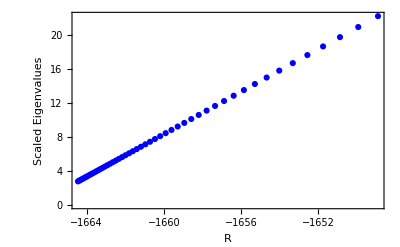

```mathematica
Clear[R,C3,Δ]

R=Range[5*10^(-9),10*10^(-9),0.1*10^(-9)];
C3=1*10^(-48);
Δ=1*10^(-21);

eigenvalues=Table[Eigenvalues[{{2*C3/R^3-Δ/3,-Sqrt[2]*Δ/3},{-Sqrt[2]*Δ/3,C3/R^3-2*Δ/3}}]//FullSimplify,{R,R}];

scaledEigenvalues=eigenvalues/(6*10^(-34)*10^9);

ListPlot[scaledEigenvalues,PlotStyle->{Red,Blue},Frame->True,FrameLabel->{"R","Scaled Eigenvalues"}]
```

```mathematica
Clear[a,b,c,d]
Clear[R,C3,Δ]
eigenvalues={{1/2 (a+d-Sqrt[a^2+4 b c-2 a d+d^2]),1/2 (a+d+Sqrt[a^2+4 b c-2 a d+d^2])}};

(*Substitute the expressions and simplify*)
simplifiedEigenvalues=eigenvalues/. {a->2*C3/R^3-Δ/3,b->-Sqrt[2]*Δ/3,c->-Sqrt[2]*Δ/3,d->C3/R^3-2*Δ/3}//FullSimplify

(*Output the simplified expressions*)
simplifiedEigenvalues
```

{{(9 C3-R^3 (3 Δ+√((9 C3^2)/R^6+(6 C3 Δ)/R^3+9 Δ^2)))/(6 R^3),(9 C3-3 R^3 Δ+R^3 √((9 C3^2)/R^6+(6 C3 Δ)/R^3+9 Δ^2))/(6 R^3)}}

{{(9 C3-R^3 (3 Δ+√((9 C3^2)/R^6+(6 C3 Δ)/R^3+9 Δ^2)))/(6 R^3),(9 C3-3 R^3 Δ+R^3 √((9 C3^2)/R^6+(6 C3 Δ)/R^3+9 Δ^2))/(6 R^3)}}

```mathematica
Clear[C3,Δ]

(*Define values for C3 and Δ*)
C3=1e-48; (*Replace with your desired value*)
Δ=1e-21; (*Replace with your desired value*)

(*Define the eigenvalues as functions of R*)
eigenvalue1[R_]:=(9 C3-R^3 (3 Δ+Sqrt[(9 C3^2)/R^6+(6 C3 Δ)/R^3+9 Δ^2]))/(6 R^3)
eigenvalue2[R_]:=(9 C3-3 R^3 Δ+R^3 Sqrt[(9 C3^2)/R^6+(6 C3 Δ)/R^3+9 Δ^2])/(6 R^3)

(*Create a list of R values*)
Rvalues=Range[5*10^(-9),10*10^(-9),0.1*10^(-9)];

(*Compute the eigenvalues for each R value*)
eigenvalues={eigenvalue1[#],eigenvalue2[#]}&/@Rvalues;

(*Plot the eigenvalues*)
ListLinePlot[eigenvalues,PlotLegends->{"Eigenvalue 1","Eigenvalue 2"},AxesLabel->{"R","Eigenvalues"}]
```

-Graphics-

```mathematica
ClearAll["Global`*"]

(*Define the matrix elements*)
C3=.;
R=.;
delta=.;

(*Define the matrix*)
matrix={{2*C3/R^3-delta/3,Sqrt[2]*delta/3},{Sqrt[2]*delta/3,-C3/R^3-2*delta/3}};

(*Compute the eigenvalues*)
eigenvalues=Expand[Eigenvalues[matrix]]
```

{-delta/2+C3/(2 R^3)-(√(9 C3^2+2 C3 delta R^3+delta^2 R^6))/(2 R^3),-delta/2+C3/(2 R^3)+(√(9 C3^2+2 C3 delta R^3+delta^2 R^6))/(2 R^3)}